```mathematica
<<SciDraw`
```

𝒮𝒸𝒾𝒟𝓇𝒶𝓌: Publication–quality scientific figures with Mathematica
M. A. Caprio, University of Notre Dame
Version 0.0.3 (February 20, 2014)
View color paletteVisit home page  -Graphics-

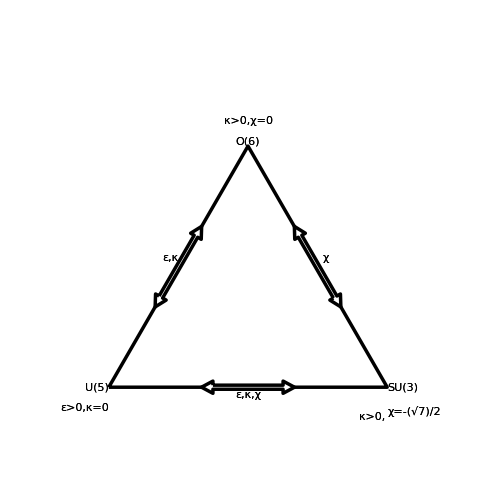

```mathematica
Figure[
FigurePanel[
{
SetOptions[FigObject,FillColor->White,LineThickness->2.5],
SetOptions[FigLabel,FontSize->22];
FigPolygon⟦"CastenTri"⟧[{{0,0},{1,0},{Cos[60*Pi/180],Sin[60*Pi/180]}}];
FigAnchor⟦"O6"⟧[{Cos[60*Pi/180],Sin[60*Pi/180]}];
FigAnchor⟦"U5"⟧[{0,0}];
FigAnchor⟦"SU3"⟧[{1,0}];
FigAnchor⟦"leftleg"⟧[{0.5*Cos[60*Pi/180],0.5*Sin[60*Pi/180]}];
FigAnchor⟦"rightleg"⟧[{0.5*Cos[60*Pi/180]+0.5,0.5*Sin[60*Pi/180]}];
FigAnchor⟦"bottomleg"⟧[{0.5,0}];
FigLabel⟦"O6_lab"⟧["O6","O(6)",TextOffset->Bottom];
FigLabel⟦"U5_lab"⟧["U5","U(5)",TextOffset->Right];
FigLabel⟦"SU3_lab"⟧["SU3","SU(3)",TextOffset->Left];
SetOptions[FigLabel,FontSize->14];
FigLabel⟦"O6_param"⟧["O6","κ>0,χ=0",TextOffset->Bottom,TextNudge->{0,25}];
FigLabel⟦"U5_param"⟧["U5","ε>0,κ=0",TextOffset->Right,TextNudge->{0,-25}];
FigLabel⟦"SU3_param1"⟧["SU3","κ>0,",TextOffset->Left,TextNudge->{-35,-37}];
FigLabel⟦"SU3_param2"⟧["SU3",RowBox[{"χ=-",√(7/4)}],TextOffset->Left,TextNudge->{0,-30}];

FigLabel⟦"leftleg1"⟧["leftleg","ε,κ",TextOrientation->60*Degree,TextNudge->{-10,10}];
FigLabel⟦"rightleg1"⟧["rightleg","χ",TextOrientation->-60*Degree,TextNudge->{10,10}];
FigLabel⟦"bottomleg1"⟧["bottomleg","ε,κ,χ",TextNudge->{0,-10}];
SetOptions[FigArrow,ArrowType->Block,HeadLength->14,TailLength->14,HeadLip->5];
FigArrow[["left_line"]][{{0.333*Cos[60*Pi/180],0.333*Sin[60*Pi/180]},{0.667*Cos[60*Pi/180],0.667*Sin[60*Pi/180]}},ShowTail->True];
FigArrow[["bottom_line"]][{{0.333,0},{0.667,0}},ShowTail->True];
FigArrow[["right_line"]][{{1-0.333*Cos[60*Pi/180],0.333*Sin[60*Pi/180]},{1-0.667*Cos[60*Pi/180],0.667*Sin[60*Pi/180]}},ShowTail->True];
(*FigLabel[["IBA_H"]][{0.5,0.25},"H=εN+κQQ"];*)
},
Frame->False,
PlotRange->{{-0.2,1.2},{-0.2,1.2}},ExtendRange->Automatic
],
CanvasSize->1.15*{6,6},CanvasMargin->0
]
```